## Bare Susceptibility calc

### Setup

#### Set Options

Automating good looking plots

```mathematica
SetOptions[ DiscretePlot,Joined-> True, Filling-> None,Frame-> True,LabelStyle->{FontSize->18,FontFamily->"Times",Black},ImageSize->Medium];
SetOptions[ ListPlot,Joined-> True, Filling-> None,Frame-> True,LabelStyle->{FontSize->18,FontFamily->"Times",Black},ImageSize->Medium,PlotStyle->{Black,Thick}];
```

#### Lattice vectors

```mathematica
a1 = {(√3)/2,1/2}; a2 = {(√3)/2,-1/2}; τ = {1/(√3),0};
```

```mathematica
LatMat = {a1,a2};
```

```mathematica
ReciLatMat = 2π Inverse[LatMat]†;
```

```mathematica
b1 = ReciLatMat[[1]] ; b2 = ReciLatMat[[2]];
```

```mathematica
GamaVec = {RotationMatrix[2 π/3].τ, RotationMatrix[4 π/3].τ, τ};
```

```mathematica
GamaVec = {RotationMatrix[2 π/3].τ-τ, RotationMatrix[4 π/3].τ-τ,{0,0}};
```

#### kSpan

kSpan : set of points for k-sums, and rSpan : set of points for r-sums

```mathematica
kSpan[krange_]:=N[Flatten[Table[i*b1+j*b2,{i,0,0.999,1/krange},{j,0,0.999,1/krange}],1]];
```

```mathematica
rSpan[range_]:=N[Flatten[Table[i*a1+j*a2,{i,-range,range},{j,-range,range}],1]];
```

```mathematica
inp[a_,b_]:= Conjugate[a].b;
```

```mathematica
kvec[k1_,k2_]:= k1 b1 + k2 b2;
```

We will play around with k-range and range to check for convergence

```mathematica
BZNorm[krange_] := 1/Length[ kSpan[krange]];
```

This is the normalization used in all k-space sums.

### TB model

#### Hopping

```mathematica
Tvec[tvec_] := { {{tvec[[3]],0,0},{0,tvec[[1]],tvec[[2]]},{0,tvec[[2]],tvec[[1]]}}, {{tvec[[1]],0,tvec[[2]]},{0,tvec[[3]],0},{tvec[[2]],0,tvec[[1]]}}, {{tvec[[1]],tvec[[2]],0},{tvec[[2]],tvec[[1]],0},{0,0,tvec[[3]]}} };
```

```mathematica
HopMat[ tvec_,k_] := Sum[ Exp[ I k.GamaVec[[i]] ] Tvec[tvec][[i]],{i,1,3}];
```

#### On-site Spin Orbit term

```mathematica
Lvec = { {{0,0,0},{0,0,-I},{0,I,0}}, {{0,0,I},{0,0,0},{-I,0,0}}, {{0,-I,0},{I,0,0},{0,0,0}} };
```

```mathematica
Jop = Sum[ KroneckerProduct[ Lvec[[i]], PauliMatrix[i]],{i,1,3}] ;
```

#### Hamiltonian

The basis is {A,d_yz↑,A,d_yz↓,A,d_xz↑,A,d_xz↓,A,d_xy↑,A,d_xy↓,B,d_yz↑,B,d_yz↓,B,d_xz↑,B,d_xz↓,B,d_xy↑,B,d_xy↓}

```mathematica
Gama = {0.,0.};
```

```mathematica
Clear[HamFM];HamFM[tvec_, λ_,Δ_,k_] := HamFM[tvec,λ,Δ,k]= KroneckerProduct[ PauliMatrix[1],Re[  HopMat[ tvec,k] ],IdentityMatrix[2] ] + KroneckerProduct[ PauliMatrix[2],Im[  HopMat[ tvec,k] ],IdentityMatrix[2] ] - λ/2 Sum[ KroneckerProduct[ IdentityMatrix[2],Lvec[[i]], PauliMatrix[i]],{i,1,3}] + Δ[[1]] KroneckerProduct[ PauliMatrix[3],IdentityMatrix[6]]+ Δ[[2]] KroneckerProduct[ IdentityMatrix[6],PauliMatrix[1]+PauliMatrix[2]+PauliMatrix[3]];
```

```mathematica
Clear[Energies];Energies[tvec_, λ_,Δ_,k_] := Energies[tvec,λ,Δ,k] =Chop[Sort[ Eigenvalues[ HamFM[tvec,λ,Δ,k] ]]];
```

```mathematica
Umat[tvec_, λ_,Δ_,k_] := Umat[tvec,λ,Δ,k] =N[Transpose[ Transpose[ SortBy[ Transpose[ Eigensystem[ HamFM[tvec,λ,Δ,k] ] ] ,First ] ][[2]]]];
```

```mathematica
UmatGS[tvec_, λ_,Δ_,k_] := UmatGS[tvec,λ,Δ,k] = Table[ If[i==j,Exp[-I Arg[  Umat[tvec,λ,Δ,Gama][[i,i]] ]],0.0],{i,1,12},{j,1,12}].Umat[tvec,λ,Δ,k];
```

```mathematica
EmV[G_]:= KroneckerProduct[ {{1,0},{0,Exp[ I G.τ]}}, IdentityMatrix[6]];
```

#### Projected Space, Band flattening

```mathematica
Proj[tvec_, λ_,Δ_,k_] := Proj[tvec,λ,Δ,k] =Module[ {U = Umat[tvec,λ,Δ,k][[All,9;;12]]}, U.U†];
```

```mathematica
Clear[ProjEn];ProjEn[tvec_, λ_,Δ_,k_] := ProjEn[tvec,λ,Δ,k] =Chop[Sort[ Eigenvalues[ Proj[tvec,λ,Δ,k] ]]];
```

```mathematica
Block[{tvec={0,0.1,0},λ=1.0,Δ={0,0}, k= {0,4}}, -1+2ProjEn[tvec,λ,Δ,k]]
```

{-1,-1,-1,-1,-1,-1,-1,-1,1.,1.,1.,1.}

```mathematica
Block[{tvec={0,0.1,0},λ=1.0,Δ={0,0}, k= {0,0}}, Eigenvectors[ Proj[tvec,λ,Δ,k]]]//Chop//MatrixForm
```

(0.517658-0.238185 ⅈ | -0.00741228+0.00360849 ⅈ | -0.238309-0.517615 ⅈ | -0.00726817+0.00246952 ⅈ | -0.000682122+0.000580927 ⅈ | -0.524469+0.24138 ⅈ | -0.0167592-0.0337668 ⅈ | -0.0534341+0.0654766 ⅈ | 0.0345626-0.0147352 ⅈ | -0.0845083-0.00211226 ⅈ | 0.000160177-0.000580358 ⅈ | 0
0.051525+0.0518668 ⅈ | 0.053911-0.222671 ⅈ | 0.0753416-0.00945607 ⅈ | 0.284817+0.0786292 ⅈ | 0.0679694-0.256806 ⅈ | -0.0000395757+0.000861937 ⅈ | 0.0318245-0.027144 ⅈ | 0.486997+0.191269 ⅈ | -0.00166596-0.0359211 ⅈ | -0.182492+0.453506 ⅈ | 0.476554+0.188839 ⅈ | 0
-0.00714703+0.0426241 ⅈ | -0.446331+0.272632 ⅈ | 0.0248092+0.0285819 ⅈ | -0.25791-0.41499 ⅈ | -0.436212+0.269226 ⅈ | 0.000647844+0.0000321725 ⅈ | -0.0737201+0.0102479 ⅈ | 0.0936465+0.208845 ⅈ | -0.0387196+0.0671292 ⅈ | -0.265727+0.128647 ⅈ | 0.111808+0.240974 ⅈ | 0
0.000982044+0.0376507 ⅈ | 0.0762834-0.0376507 ⅈ | -0.0376507-0.000982044 ⅈ | 0.0762834+0.0376507 ⅈ | 0 | 0 | -0.569757-0.0000865288 ⅈ | 0.00742026+0.0000865288 ⅈ | 0.0000865288+0.569757 ⅈ | 0.00742026-0.0000865288 ⅈ | 0 | 0.57735
-0.219907+0.0357747 ⅈ | -0.213207-0.00377459 ⅈ | 0.0576104-0.0601934 ⅈ | -0.0233044+0.137237 ⅈ | 0.0909975+0.0439782 ⅈ | -0.227895+0.0264587 ⅈ | -0.252497-0.00703765 ⅈ | 0.645044+0.0274894 ⅈ | 0.0298314-0.236784 ⅈ | -0.00565626-0.106079 ⅈ | -0.512155-0.0673379 ⅈ | 0
0.0739078+0.103337 ⅈ | 0.0725027-0.000742294 ⅈ | -0.0128658+0.198934 ⅈ | 0.0588919-0.252743 ⅈ | 0.200929+0.0609286 ⅈ | -0.116026+0.00527694 ⅈ | -0.545748-0.0568435 ⅈ | -0.301536+0.0643599 ⅈ | 0.0103395-0.552269 ⅈ | 0.158763+0.281632 ⅈ | 0.0207021+0.0879902 ⅈ | 0
-0.00069441-0.0266231 ⅈ | -0.0539405+0.0266231 ⅈ | 0.0266231+0.00069441 ⅈ | -0.0539405-0.0266231 ⅈ | 0 | 0 | 0.402879+0.0000611851 ⅈ | -0.00524691-0.0000611851 ⅈ | -0.0000611851-0.402879 ⅈ | -0.00524691+0.0000611851 ⅈ | 0 | 0.816497
0.440045+0.187342 ⅈ | 0.377106+0.215979 ⅈ | -0.14167+0.298112 ⅈ | 0.116167+0.0173083 ⅈ | -0.387618-0.0456081 ⅈ | 0.144325+0.0383225 ⅈ | -0.107119-0.0222207 ⅈ | 0.25799+0.0522338 ⅈ | 0.0179677-0.183901 ⅈ | -0.118752-0.353916 ⅈ | 0.0426355-0.168733 ⅈ | 0
0.166388+0.225018 ⅈ | -0.0574469-0.253922 ⅈ | -0.207629-0.105965 ⅈ | -0.373873-0.402716 ⅈ | 0.482555-0.088422 ⅈ | 0.303378+0.0389659 ⅈ | -0.0162979-0.124391 ⅈ | 0.153274-0.104314 ⅈ | 0.0495476+0.0233781 ⅈ | -0.244935-0.188642 ⅈ | 0.0584233-0.106134 ⅈ | 0
-0.402334-0.193041 ⅈ | 0.445207+0.255457 ⅈ | -0.072133-0.402682 ⅈ | -0.059251-0.295363 ⅈ | -0.123604-0.307959 ⅈ | 0.00849794-0.290225 ⅈ | -0.104308+0.106396 ⅈ | 0.0178832-0.0219122 ⅈ | -0.0256765-0.109107 ⅈ | -0.2068+0.0260078 ⅈ | -0.005167-0.076401 ⅈ | 0
-0.0421557+0.182873 ⅈ | -0.126178-0.139063 ⅈ | 0.0811136-0.478252 ⅈ | 0.0330755+0.357784 ⅈ | -0.207263+0.165191 ⅈ | 0.465212+0.211596 ⅈ | -0.210879+0.105429 ⅈ | -0.161864+0.0410433 ⅈ | -0.0503739-0.234156 ⅈ | -0.186528+0.075799 ⅈ | 0.0473645-0.223729 ⅈ | 0
-0.189861-0.150727 ⅈ | -0.20269-0.126007 ⅈ | -0.229682+0.0241014 ⅈ | 0.0283286+0.199782 ⅈ | 0.0378425+0.193822 ⅈ | -0.188255-0.322099 ⅈ | -0.17362+0.0619871 ⅈ | 0.0140361-0.148969 ⅈ | -0.0652868-0.175939 ⅈ | -0.0711887-0.476283 ⅈ | 0.53244+0.0709832 ⅈ | 0)

```mathematica
Block[{tvec={0,0.1,0},λ=1.0,Δ={0,0}, k= {0,0}}, Umat[tvec,λ,Δ,k]]//Chop//MatrixForm
```

(0.273361-0.0796124 ⅈ | -0.129176-0.262519 ⅈ | 0.274606+0.237032 ⅈ | 0.175897+0.0642995 ⅈ | -0.266519-0.093027 ⅈ | -0.162962+0.245812 ⅈ | 0.327787+0.152155 ⅈ | 0.128054-0.140261 ⅈ | 0.0612718-0.0498915 ⅈ | 0.399205+0.0325355 ⅈ | 0.0386045+0.0471843 ⅈ | 0.402844-0.0258204 ⅈ
0.284012+0.0702824 ⅈ | -0.0195464+0.284046 ⅈ | -0.112301-0.149875 ⅈ | 0.306164+0.194567 ⅈ | -0.23193+0.182177 ⅈ | -0.114131-0.258187 ⅈ | -0.0137901-0.189423 ⅈ | 0.351642+0.0833267 ⅈ | 0.116602+0.38318 ⅈ | 0.0357357-0.0704724 ⅈ | 0.36395+0.174615 ⅈ | -0.0534502+0.0293213 ⅈ
0.115285-0.0697414 ⅈ | 0.18021-0.340641 ⅈ | -0.237032-0.112301 ⅈ | -0.0642995+0.306164 ⅈ | 0.184509-0.134214 ⅈ | -0.258511+0.218591 ⅈ | -0.152155-0.0137901 ⅈ | 0.140261+0.351642 ⅈ | -0.0392041-0.0872866 ⅈ | -0.0223941-0.396244 ⅈ | 0.064399+0.00385031 ⅈ | 0.0275816-0.402174 ⅈ
0.294428-0.248645 ⅈ | -0.0435794+0.127496 ⅈ | -0.274606+0.149875 ⅈ | -0.175897-0.194567 ⅈ | -0.197124+0.275231 ⅈ | -0.118962+0.194691 ⅈ | -0.327787+0.189423 ⅈ | -0.128054-0.0833267 ⅈ | -0.391956+0.0622974 ⅈ | 0.0936228+0.0197655 ⅈ | -0.124838+0.383301 ⅈ | -0.0611652-0.0205152 ⅈ
0.0345866+0.158617 ⅈ | -0.0798029-0.365982 ⅈ | -0.0375735-0.124731 ⅈ | -0.111597-0.370463 ⅈ | -0.0324749-0.403065 ⅈ | 0.00450808+0.0559523 ⅈ | -0.175633-0.138365 ⅈ | -0.268315-0.211381 ⅈ | 0.0861742+0.39637 ⅈ | -0.00980885-0.0451171 ⅈ | 0.378572+0.152671 ⅈ | 0.00597535+0.00240975 ⅈ
0.374581 | 0.162344 | 0.386907 | -0.130267 | -0.0561336 | -0.404371 | 0.341577 | -0.223588 | -0.0461711 | -0.405629 | 0.00644296 | -0.408197
-0.273361+0.0796124 ⅈ | 0.129176+0.262519 ⅈ | 0.274606+0.237032 ⅈ | 0.175897+0.0642995 ⅈ | -0.266519-0.093027 ⅈ | -0.162962+0.245812 ⅈ | -0.327787-0.152155 ⅈ | -0.128054+0.140261 ⅈ | -0.0612718+0.0498915 ⅈ | -0.399205-0.0325355 ⅈ | 0.0386045+0.0471843 ⅈ | 0.402844-0.0258204 ⅈ
-0.284012-0.0702824 ⅈ | 0.0195464-0.284046 ⅈ | -0.112301-0.149875 ⅈ | 0.306164+0.194567 ⅈ | -0.23193+0.182177 ⅈ | -0.114131-0.258187 ⅈ | 0.0137901+0.189423 ⅈ | -0.351642-0.0833267 ⅈ | -0.116602-0.38318 ⅈ | -0.0357357+0.0704724 ⅈ | 0.36395+0.174615 ⅈ | -0.0534502+0.0293213 ⅈ
-0.115285+0.0697414 ⅈ | -0.18021+0.340641 ⅈ | -0.237032-0.112301 ⅈ | -0.0642995+0.306164 ⅈ | 0.184509-0.134214 ⅈ | -0.258511+0.218591 ⅈ | 0.152155+0.0137901 ⅈ | -0.140261-0.351642 ⅈ | 0.0392041+0.0872866 ⅈ | 0.0223941+0.396244 ⅈ | 0.064399+0.00385031 ⅈ | 0.0275816-0.402174 ⅈ
-0.294428+0.248645 ⅈ | 0.0435794-0.127496 ⅈ | -0.274606+0.149875 ⅈ | -0.175897-0.194567 ⅈ | -0.197124+0.275231 ⅈ | -0.118962+0.194691 ⅈ | 0.327787-0.189423 ⅈ | 0.128054+0.0833267 ⅈ | 0.391956-0.0622974 ⅈ | -0.0936228-0.0197655 ⅈ | -0.124838+0.383301 ⅈ | -0.0611652-0.0205152 ⅈ
-0.0345866-0.158617 ⅈ | 0.0798029+0.365982 ⅈ | -0.0375735-0.124731 ⅈ | -0.111597-0.370463 ⅈ | -0.0324749-0.403065 ⅈ | 0.00450808+0.0559523 ⅈ | 0.175633+0.138365 ⅈ | 0.268315+0.211381 ⅈ | -0.0861742-0.39637 ⅈ | 0.00980885+0.0451171 ⅈ | 0.378572+0.152671 ⅈ | 0.00597535+0.00240975 ⅈ
-0.374581 | -0.162344 | 0.386907 | -0.130267 | -0.0561336 | -0.404371 | -0.341577 | 0.223588 | 0.0461711 | 0.405629 | 0.00644296 | -0.408197)

#### Plot Band Structure

```mathematica
Gama = {0,0}; Kpoint =-b1/3+b2/3; Mpoint = -b1/2;
```

```mathematica
BetAB[ a_, b_] = Table[ (1-i)*a +i*b , {i,0.,1,0.01}];
```

```mathematica
kCut = Join[BetAB[ Gama,Kpoint]  ,BetAB[Kpoint,Mpoint], BetAB[Mpoint,-Kpoint],BetAB[-Kpoint,Gama] ];
```

```mathematica
PlotDispData[tvec_, λ_,Δ_] := Table[ Energies[tvec,λ,Δ,k]  ,{k,kCut} ];
```

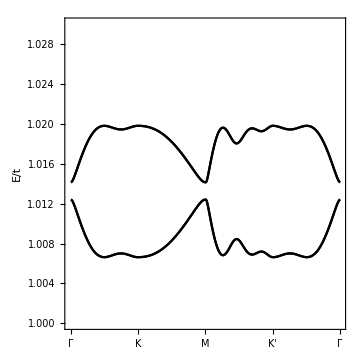

```mathematica
Block[ {tvec={0.0,0.1,0.0},λ=1.0,Δ={0,0}},ListPlot[Table[ PlotDispData[tvec,λ,Δ][[All,i]],{i,1,12}],PlotStyle->Black,
FrameTicks->{{{1,"Γ"},{101,"K"},{202,"M"},{303,"K'"},{404,"Γ"}},Automatic},Joined->True,FrameLabel->{None,"E/t"},AspectRatio->1/1,PlotRange->{1.0,1.03}]]
```

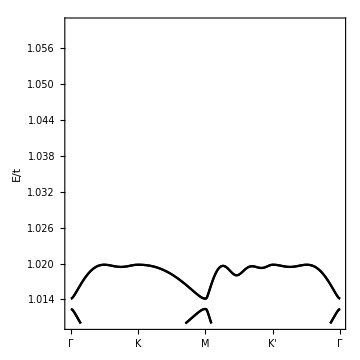

```mathematica
Block[ {tvec={0.0,0.1,0.0},λ=1.0,Δ={0,0}},ListPlot[Table[ PlotDispData[tvec,λ,Δ][[All,i]],{i,1,12}],PlotStyle->Black,
FrameTicks->{{{1,"Γ"},{101,"K"},{202,"M"},{303,"K'"},{404,"Γ"}},Automatic},Joined->True,FrameLabel->{None,"E/t"},AspectRatio->1/1,PlotRange->{1.01,1.06}]]
```

### Wannier Functions

#### Guess for WFs

```mathematica
bandRange =Range[9,12];
```

```mathematica
Clear[guess];guess[tvec_,λ_,Δ_]:=Transpose[Umat[tvec,λ,Δ,Gama][[All,bandRange]]];
```

```mathematica
Clear[waveF,SmatWF];waveF[tvec_,λ_,Δ_,k_] :=waveF[tvec,λ,Δ,k]=Module[ {um =  Umat[tvec,λ,Δ,k], gs =guess[tvec,λ,Δ] },  Table[Sum[um[[All,i]]inp[um[[All,i]],gs[[nm]]],{i,bandRange}], {nm,1,Length[bandRange]}]];
```

```mathematica
SmatWF[tvec_,λ_,Δ_,k_] := SmatWF[tvec,λ,Δ,k]=Table[ inp[ waveF[tvec,λ,Δ,k][[m]], waveF[tvec,λ,Δ,k][[n]]],{m,1,Length[bandRange]},{n,1,Length[bandRange]}]
```

```mathematica
Block[ {tvec={0,0.1,0}, λ=1, Δ={0,0}},{ Det[SmatWF[tvec,λ,Δ,Gama]],Det[SmatWF[tvec,λ,Δ,Kpoint]],Det[SmatWF[tvec,λ,Δ,-Kpoint]],Det[SmatWF[tvec,λ,Δ,Mpoint]]}]//Chop
```

{1.,0.932201,0.932201,0.954054}

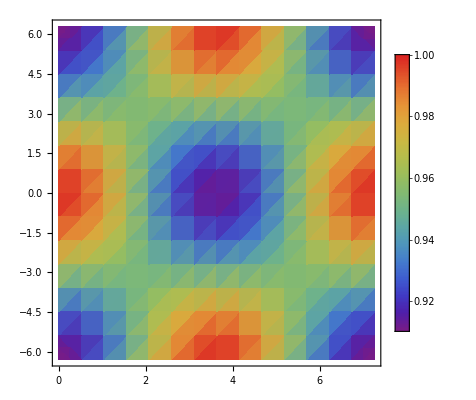

```mathematica
Block[{ tvec={0,0.1,0},λ=1,Δ={0.0,0.0}}, DensityPlot[Chop[ Det[SmatWF[tvec,λ,Δ,{kx,ky}]]],{kx,0,4 π/(√3)},{ky,-2π,2π},PlotLegends->Automatic,ColorFunction->"Rainbow",PlotRange->All]]
```

```mathematica
Clear[MinDet];MinDet[tvec_,λ_,Δ_]:=MinDet[tvec,λ,Δ]=Min[Table[Abs[ Det[SmatWF[tvec,λ,Δ,k]]],{k,kSpan[100]}]];
```

```mathematica
Clear[MaxMinDet];MaxMinDet[tvec_,λ_,Δ_]:=MaxMinDet[tvec,λ,Δ]=Max[Table[Abs[ Det[SmatWF[tvec,λ,Δ,k]]],{k,kSpan[100]}]]/Min[Table[Abs[ Det[SmatWF[tvec,λ,Δ,k]]],{k,kSpan[100]}]];
```

```mathematica
{MinDet[{0,0.1,0},1,{0,0}],MaxMinDet[{0,0.1,0},1,{0,0}]}
```

{0.91027,1.09858}

```mathematica
Clear[SmatWFhf,Psi]
```

```mathematica
SmatWFhf[tvec_,λ_,Δ_,k_] := MatrixPower[ SmatWF[tvec,λ,Δ,k],-0.5];
```

```mathematica
Psi[tvec_,λ_,Δ_,k_]:= Psi[tvec,λ,Δ,k]=Module[ {mat =  SmatWFhf[tvec,λ,Δ,k]}, Table[ Sum[ mat[[i,j]] waveF[tvec,λ,Δ,k][[i]],{i,1,Length[bandRange]}],{ j,1,Length[bandRange]}]];
```

```mathematica
Psi2[tvec_,λ_,Δ_,k_]:= Psi2[tvec,λ,Δ,k]=Orthogonalize[waveF[tvec,λ,Δ,k]]
```

```mathematica
Block[ {tvec={0,0.1,0},λ=1,Δ={0,0},k={0.5,0.4}},  Psi2[tvec,λ,Δ,k]]//MatrixForm
```

(0.0772461-0.0490885 ⅈ | 0.115948+0.386389 ⅈ | -0.0330354-0.0878334 ⅈ | -0.391794+0.0623258 ⅈ | 0.0840698+0.394677 ⅈ | -0.0287599+0.00729486 ⅈ | -0.0472478+0.0406873 ⅈ | -0.115928-0.380644 ⅈ | 0.0451869+0.0858063 ⅈ | 0.392247-0.0622746 ⅈ | -0.0901426-0.397041 ⅈ | 0.0619767-0.00259516 ⅈ
0.396583+0.0324154 ⅈ | 0.029721-0.0548131 ⅈ | -0.0224782-0.396523 ⅈ | 0.0934473+0.0259262 ⅈ | -0.0106308-0.0611133 ⅈ | -0.407128-0.00373509 ⅈ | -0.402201-0.0312144 ⅈ | -0.0315574+0.0859115 ⅈ | 0.0223319+0.396091 ⅈ | -0.0928466-0.0136215 ⅈ | -0.00101841+0.0296532 ⅈ | 0.403528-0.00169676 ⅈ
0.0268+0.0595189 ⅈ | 0.365233+0.175171 ⅈ | 0.0617215+0.0093246 ⅈ | -0.125135+0.382888 ⅈ | 0.377403+0.154241 ⅈ | -0.00951449+0.0092872 ⅈ | 0.0406965+0.0311321 ⅈ | 0.363209+0.17449 ⅈ | 0.0653769-0.0023943 ⅈ | -0.124603+0.383887 ⅈ | 0.379412+0.150185 ⅈ | 0.0136449-0.0154326 ⅈ
0.40211-0.0259814 ⅈ | -0.0493867+0.0136516 ⅈ | 0.0280186-0.402629 ⅈ | -0.0597366-0.0266723 ⅈ | 0.00688265+0.0194159 ⅈ | -0.408046-0.00261939 ⅈ | 0.404242-0.025856 ⅈ | -0.0471158+0.0451757 ⅈ | 0.027152-0.401902 ⅈ | -0.0607295-0.0144368 ⅈ | -0.00535043-0.0121717 ⅈ | -0.407701+0.00189371 ⅈ)

```mathematica
Block[ {tvec={0,0.1,0},λ=1,Δ={0,0},k={0.5,0.4}},  Psi[tvec,λ,Δ,k]]//MatrixForm
```

(0.0772489-0.0490916 ⅈ | 0.11594+0.386374 ⅈ | -0.0330374-0.0878374 ⅈ | -0.39178+0.0623167 ⅈ | 0.0840618+0.394662 ⅈ | -0.0287615+0.00729518 ⅈ | -0.0472462+0.0406848 ⅈ | -0.115935-0.380658 ⅈ | 0.0451845+0.0858025 ⅈ | 0.392261-0.0622836 ⅈ | -0.0901508-0.397056 ⅈ | 0.0619738-0.00259463 ⅈ
0.396599+0.0324193 ⅈ | 0.0297188-0.054811 ⅈ | -0.0224723-0.396539 ⅈ | 0.0934431+0.0259247 ⅈ | -0.0106307-0.0611103 ⅈ | -0.407145-0.00373998 ⅈ | -0.402185-0.0312104 ⅈ | -0.0315598+0.0859148 ⅈ | 0.0223378+0.396076 ⅈ | -0.092851-0.0136226 ⅈ | -0.00101839+0.0296548 ⅈ | 0.403512-0.00170141 ⅈ
0.0268002+0.0595172 ⅈ | 0.365247+0.175181 ⅈ | 0.0617201+0.00932341 ⅈ | -0.125146+0.382901 ⅈ | 0.377416+0.154252 ⅈ | -0.00951432+0.00928622 ⅈ | 0.0406971+0.0311328 ⅈ | 0.363195+0.17448 ⅈ | 0.0653787-0.00239348 ⅈ | -0.124592+0.383874 ⅈ | 0.379398+0.150175 ⅈ | 0.013646-0.0154323 ⅈ
0.402093-0.0259779 ⅈ | -0.0493875+0.013652 ⅈ | 0.0280242-0.402613 ⅈ | -0.0597385-0.0266722 ⅈ | 0.00688372+0.019416 ⅈ | -0.40803-0.002624 ⅈ | 0.404258-0.0258596 ⅈ | -0.0471153+0.045174 ⅈ | 0.0271463-0.401918 ⅈ | -0.0607277-0.0144373 ⅈ | -0.00535064-0.0121707 ⅈ | -0.407717+0.00189844 ⅈ)

```mathematica
Block[ {tvec={0,0.1,0},λ=1,Δ={0,0},k=RandomReal[]b1 + RandomReal[]b2},  Psi[tvec,λ,Δ,k].Psi[tvec,λ,Δ,k]†]//MatrixForm//Chop
```

(1. | 0 | 0 | 0
0 | 1. | 0 | 0
0 | 0 | 1. | 0
0 | 0 | 0 | 1.)

```mathematica
Block[ {tvec={0,0.1,0},λ=1,Δ={0,0},k=RandomReal[]b1 + RandomReal[]b2},  Psi2[tvec,λ,Δ,k].Psi2[tvec,λ,Δ,k]†]//MatrixForm//Chop
```

(1. | 0 | 0 | 0
0 | 1. | 0 | 0
0 | 0 | 1. | 0
0 | 0 | 0 | 1.)

#### Smooth phase of Psi

```mathematica
Clear[waveFC,VecPotPsi1,VPsi1Sq,VPsi1Sum];
```

```mathematica
waveFC[tvec_,λ_,Δ_,k_] :=waveFC[tvec,λ,Δ,k]= Psi[tvec,λ,Δ,k][[4]];
```

```mathematica
VecPotPsi1[tvec_,λ_,Δ_,k_,n_,dn_]:= VecPotPsi1[tvec,λ,Δ,k,n,dn]=I inp[ Conjugate[waveFC[tvec,λ,Δ,k]],1/dn( waveFC[tvec,λ,Δ,k+dn n]-waveFC[tvec,λ,Δ,k])];
```

```mathematica
VPsi1Sq[tvec_,λ_,Δ_,k_,dn_] :=VPsi1Sq[tvec,λ,Δ,k,dn]= Norm[ { VecPotPsi1[tvec,λ,Δ,k,{1,0},dn], VecPotPsi1[tvec,λ,Δ,k,{0,1},dn]}]^2;
```

```mathematica
VPsi1Sum[tvec_,λ_,Δ_,krange_,dn_] :=VPsi1Sum[tvec,λ,Δ,krange,dn]= 1/Length[kSpan[krange]] Sum[ VPsi1Sq[tvec,λ,Δ,k,dn],{k,kSpan[krange]}];
```

```mathematica
Block[{ tvec={0,0.1,0},λ=1,dn = 0.01,Δ={0.0,0.0},krange=100},VPsi1Sum[tvec,λ,Δ,krange,dn]]
```

0.0000501816

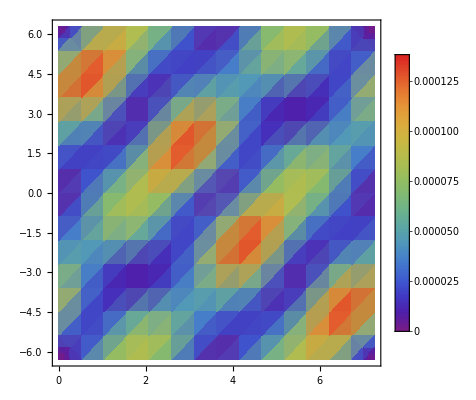

```mathematica
Block[{ tvec={0,0.1,0},λ=1,dn = 0.01,Δ={0.0,0.0}}, DensityPlot[ VPsi1Sq[tvec,λ,Δ,{kx,ky},dn],{kx,0,4 π/(√3)},{ky,-2π,2π},PlotLegends->Automatic,ColorFunction->"Rainbow",PlotRange->All]]
```

#### Wannier definitions

For Psi

```mathematica
Clear[WanFuPsi,WFAmpPsi,OmegaPsi]
```

```mathematica
WanFuPsi[tvec_,λ_,Δ_,r_,krange_,band_] := WanFuPsi[tvec,λ,Δ,r,krange,band]=1/Length[kSpan[krange]] Sum[Exp[-I k.r]  Psi[tvec,λ,Δ,k][[band]] ,{k,kSpan[krange]}]
```

now it’s amplitude

```mathematica
WFAmpPsi[tvec_,λ_,Δ_,r_,krange_,band_] := WFAmpPsi[tvec,λ,Δ,r,krange,band] =  Norm[WanFuPsi[tvec,λ,Δ,r,krange,band ]]^2;
```

```mathematica
OmegaPsi[ tvec_,λ_,Δ_,range_,krange_,band_] := OmegaPsi[tvec,λ,Δ,range,krange,band] =  Sum[ Norm[r]^2 WFAmpPsi[tvec,λ,Δ,r,krange,band] ,{r,rSpan[range]}]- Norm[Sum[r  WFAmpPsi[tvec,λ,Δ,r,krange,band] ,{r,rSpan[range]}]]^2;
```

#### Wannier Functions: Checks

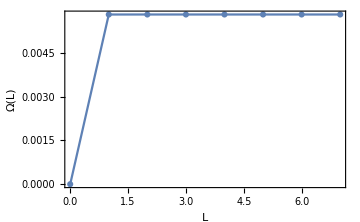

```mathematica
Block[ {tvec={0,0.1,0},λ=1,krange=50,Δ={0,0},band=1},DiscretePlot[ OmegaPsi[tvec,λ,Δ,range,krange,band] , {range,0,7}, FrameLabel->{"L","Ω(L)"},PlotMarkers->Automatic] ]
```

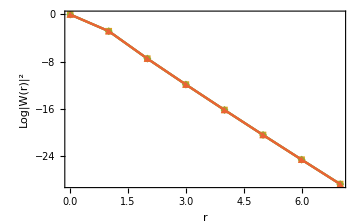

```mathematica
Block[ {tvec={0,0.1,0},λ=1,krange=50,Δ={0,0},band=4},DiscretePlot[ {Log10[WFAmpPsi[tvec,λ,Δ,r a2,krange,1] ],Log10[WFAmpPsi[tvec,λ,Δ,r a2,krange,2] ],Log10[WFAmpPsi[tvec,λ,Δ,r a2,krange,3] ],Log10[WFAmpPsi[tvec,λ,Δ,r a2,krange,4] ]}, {r,0,7.0}, FrameLabel->{"r","Log|W(r)|^2"},PlotRange->{Automatic,Full},PlotMarkers->Automatic] ]
```

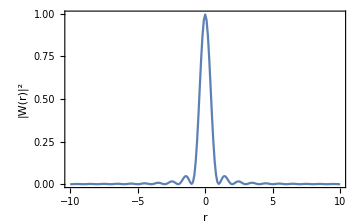

```mathematica
Block[ {tvec={0,0.1,0},λ=1,krange=50,Δ={0,0},band=4},DiscretePlot[ WFAmpPsi[tvec,λ,Δ,r a1,krange,1] , {r,-10,10.0,0.1}, FrameLabel->{"r","|W(r)|^2"},PlotRange->{Automatic,Full}] ]
```

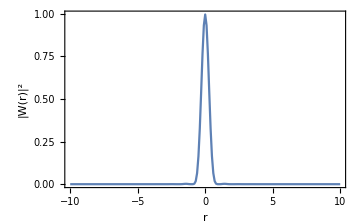

```mathematica
Block[ {tvec={0,0.1,0},λ=1,krange=50,Δ={0,0},band=4},DiscretePlot[ WFAmpPsi[tvec,λ,Δ,r (a1+a2),krange,1] , {r,-10,10.0,0.1}, FrameLabel->{"r","|W(r)|^2"},PlotRange->{Automatic,Full}] ]
```

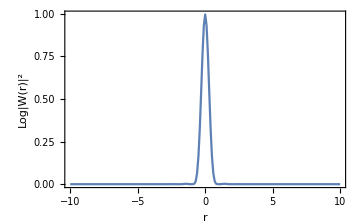

```mathematica
Block[ {tvec={0,0.1,0},λ=1,krange=50,Δ={0,0},band=4},DiscretePlot[ WFAmpPsi[tvec,λ,Δ,r (a1-a2),krange,1] , {r,-10,10.0,0.1}, FrameLabel->{"r","Log|W(r)|^2"},PlotRange->{Automatic,Full}] ]
```

```mathematica
Block[ {tvec={0,0.1,0},λ=1,krange=50,Δ={0,0},L=2},{DensityPlot[ WFAmpPsi[tvec,λ,Δ,{x,y},krange,1] , {x,-L,L},{y,-L,L},PlotLegends->Automatic,PlotRange->All,AspectRatio->1],DensityPlot[ WFAmpPsi[tvec,λ,Δ,{x,y},krange,2] , {x,-L,L},{y,-L,L},PlotLegends->Automatic,PlotRange->All,AspectRatio->1],DensityPlot[ WFAmpPsi[tvec,λ,Δ,{x,y},krange,3] , {x,-L,L},{y,-L,L},PlotLegends->Automatic,PlotRange->All,AspectRatio->1],DensityPlot[ WFAmpPsi[tvec,λ,Δ,{x,y},krange,4] , {x,-L,L},{y,-L,L},PlotLegends->Automatic,PlotRange->All,AspectRatio->1]} ]
```

$Aborted

There is no spatial structure for any Wannier Function.

#### Wannier Functions: Decomposition

Reminder: Basis is {A,d_yz↑,A,d_yz↓,A,d_xz↑,A,d_xz↓,A,d_xy↑,A,d_xy↓,B,d_yz↑,B,d_yz↓,B,d_xz↑,B,d_xz↓,B,d_xy↑,B,d_xy↓}

```mathematica
Block[ {tvec={0,0.1,0},λ=1,krange=50,Δ={0,0}},Image[Table[ Abs[WanFuPsi[tvec,λ,Δ,{0,0},krange,band][[i]]]^2,{i,1,12},{band,1,4}],ImageSize->Large] ]
```

-Graphics-

```mathematica
Block[ {tvec={0,0.1,0},λ=1,krange=50,Δ={0,0}},Table[ Sum[Abs[WanFuPsi[tvec,λ,Δ,{0,0},krange,band][[i]]]^2,{i,j,12,2}],{j,1,2},{band,1,4}] ]//MatrixForm
```

(0.34054 | 0.653643 | 0.333554 | 0.660629
0.653643 | 0.34054 | 0.660629 | 0.333554)

Rows: spin, Column: band. Spin splitting seems to occur in pairs.

```mathematica
Block[ {tvec={0,0.1,0},λ=1,krange=50,Δ={0,0}},Table[ Sum[Abs[WanFuPsi[tvec,λ,Δ,{0,0},krange,band][[i]]]^2,{i,j,j+5}],{j,1,7,6},{band,1,4}] ]//MatrixForm
```

Rows: orbital (A/B), Column: band. Every WF is evenly split on A and B sub-lattices.

Now, in J basis:

```mathematica
Amat = 1/(√6){{-√3,0,1,0,0,-√2},{0,-1,0,√3,-√2,0},{- I √3,0,-I,0,0,I √2},{0,-I,0,-I √3, -I √2,0},{0,2,0,0,-√2,0},{0,0,2,0,0,√2}};Amat2I =KroneckerProduct[ IdentityMatrix[2], Amat];
```

```mathematica
Block[ {tvec={0,0.1,0},λ=1,krange=50,Δ={0,0}},Image[Table[ Abs[inp[Amat2I[[All,i]], WanFuPsi[tvec,λ,Δ,{0,0},krange,band] ]]^2,{i,1,12},{band,1,4}],ImageSize->Large] ]
```

-Graphics-

```mathematica
Block[ {tvec={0,0.1,0},λ=1,krange=50,Δ={0,0}},Chop[Table[ inp[Amat2I[[All,i]], WanFuPsi[tvec,λ,Δ,{0,0},krange,band] ],{i,1,12},{band,1,4}],10^-2] ]//MatrixForm
```

(0 | 0.-0.0374606 ⅈ | 0 | 0.+0.0378662 ⅈ
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0.0365401 | 0 | -0.01411+0.0351391 ⅈ | 0
-0.152874-0.676224 ⅈ | -0.0254136+0.119786 ⅈ | -0.650258-0.261115 ⅈ | 0.0403688-0.0547539 ⅈ
-0.111653+0.0502816 ⅈ | -0.693266 | -0.0169604-0.0658785 ⅈ | -0.700725
0 | 0.+0.0374606 ⅈ | 0 | 0.+0.0378662 ⅈ
0 | 0 | 0 | 0
0 | 0 | 0 | 0
-0.0365401 | 0 | -0.01411+0.0351391 ⅈ | 0
0.152874+0.676224 ⅈ | 0.0254136-0.119786 ⅈ | -0.650258-0.261115 ⅈ | 0.0403688-0.0547539 ⅈ
0.111653-0.0502816 ⅈ | 0.693266 | -0.0169604-0.0658785 ⅈ | -0.700725)

It looks like a linear combination of orbitals at A and B sites. It is mostly made of j=1/2, with very small fractions from j=3/2. We can check that explicitly:

```mathematica
ran[j_]:= If[j==1, Join[Range[1,4], Range[7,10]], Join[Range[5,6], Range[11,12]]];
```

```mathematica
Block[ {tvec={0,0.1,0},λ=1,krange=50,Δ={0,0}},Table[ Sum[Abs[inp[Amat2I[[All,i]], WanFuPsi[tvec,λ,Δ,{0,0},krange,band] ]]^2,{i,ran[j]}],{j,1,2},{band,1,4}] ]//MatrixForm
```

(0.00289395 | 0.00289395 | 0.00289506 | 0.00289506
0.991289 | 0.991289 | 0.991288 | 0.991288)

Rows : J (3/2 or 1/2), Column : band. All WFs are mostly made of j=1/2 states (~ 99%)

### Hartree Correction

#### Hartree in Momentum Space

```mathematica
Clear[HFkspace];HFkspace[tvec_,λ_,Δ_,k_,krange_,band_]:= HFkspace[tvec,λ,Δ,k,krange,band] = 1/Length[kSpan[krange]] Sum[Conjugate[ Umat[tvec,λ,Δ,p][[filledband,α]]] Umat[tvec,λ,Δ,p][[filledband,α]]Conjugate[ Umat[tvec,λ,Δ,k][[band,α+1]]] Umat[tvec,λ,Δ,k][[band,α+1]] ,{α,1,12,2},{p,kSpan[krange]},{filledband,1,8}]
```

```mathematica
Block[ {tvec={0.0,0.1,0.0},λ=1.0,Δ={0,0}, krange=100,band =9},HFkspace[tvec,λ,Δ,Mpoint,krange,band]]
```

0.52453+0. ⅈ

```mathematica
Block[ {tvec={0.0,0.1,0.0},λ=1.0,Δ={0,0}, krange=100,band =9},DensityPlot[ HFkspace[tvec,λ,Δ,{kx,ky},krange,band],{kx,0,2π},{ky,0,2π},PlotLegends->Automatic]]
```

$Aborted

```mathematica
{kx,ky}
```

{0.448799,2.24399}

```mathematica
PlotDispData[tvec_, λ_,Δ_,krange_] := Table[HFkspace[tvec,λ,Δ,k,krange,9] ,{k,kCut} ];
```

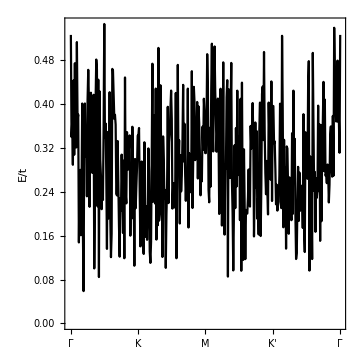

```mathematica
Block[ {tvec={0.0,0.1,0.0},λ=1.0,Δ={0,0},krange=50},ListPlot[PlotDispData[tvec,λ,Δ,krange],PlotStyle->Black,
FrameTicks->{{{1,"Γ"},{101,"K"},{202,"M"},{303,"K'"},{404,"Γ"}},Automatic},Joined->True,FrameLabel->{None,"E/t"},AspectRatio->1/1,PlotRange->All]]
```

```mathematica
Clear[HFkspaceGS];HFkspaceGS[tvec_,λ_,Δ_,k_,krange_,band_]:= HFkspaceGS[tvec,λ,Δ,k,krange,band] = 1/Length[kSpan[krange]] Sum[Conjugate[ UmatGS[tvec,λ,Δ,p][[filledband,α]]] UmatGS[tvec,λ,Δ,p][[filledband,α]]Conjugate[ UmatGS[tvec,λ,Δ,k][[band,α+1]]] UmatGS[tvec,λ,Δ,k][[band,α+1]] ,{α,1,12,2},{p,kSpan[krange]},{filledband,1,8}]
```

```mathematica
Block[ {tvec={0.0,0.1,0.0},λ=1.0,Δ={0,0}, krange=100,band =9},HFkspaceGS[tvec,λ,Δ,Mpoint,krange,band]]
```

0.52453+0. ⅈ

```mathematica
PlotDispDataGS[tvec_, λ_,Δ_,krange_] := Table[HFkspaceGS[tvec,λ,Δ,k,krange,9] ,{k,kCut} ];
```

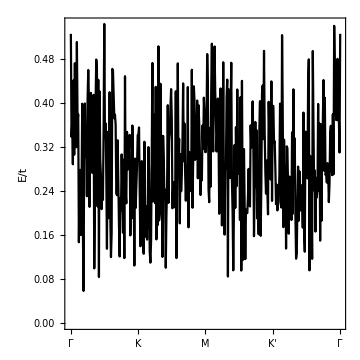

```mathematica
Block[ {tvec={0.0,0.1,0.0},λ=1.0,Δ={0,0},krange=25},ListPlot[PlotDispDataGS[tvec,λ,Δ,krange],PlotStyle->Black,
FrameTicks->{{{1,"Γ"},{101,"K"},{202,"M"},{303,"K'"},{404,"Γ"}},Automatic},Joined->True,FrameLabel->{None,"E/t"},AspectRatio->1/1,PlotRange->All]]
```

```mathematica
Block[ {tvec={0.0,0.1,0.0},λ=1.0,Δ={0,0},krange=50},ListPlot[PlotDispDataGS[tvec,λ,Δ,krange],PlotStyle->Black,
FrameTicks->{{{1,"Γ"},{101,"K"},{202,"M"},{303,"K'"},{404,"Γ"}},Automatic},Joined->True,FrameLabel->{None,"E/t"},AspectRatio->1/1,PlotRange->All]]
```

-Graphics-

#### Hartree Real Space

```mathematica
Block[ {tvec = {0.,1,0.},λ=1.0,Δ={0.0,0.0}, krange=50}, 1/Length[kSpan[krange]] Sum[ Module[ {U = Umat[tvec,λ,Δ,k][[All,1;;10]]}, U.U†],{k,kSpan[krange]}]]//MatrixForm//Chop
```

(0.833333 | 0 | 0.-0.071193 ⅈ | 0 | 0 | 0.071193 | -0.00550625-0.0106748 ⅈ | 0 | 0.0518226+0.0894176 ⅈ | -0.00640197+0.0233363 ⅈ | -0.0165918-0.0504303 ⅈ | -0.0270799+0.0120019 ⅈ
0 | 0.833333 | 0 | 0.+0.071193 ⅈ | -0.071193 | 0 | 0 | -0.00550625-0.0106748 ⅈ | -0.0233363-0.00640197 ⅈ | 0.0439299+0.0934786 ⅈ | -0.0240105+0.0153045 ⅈ | -0.0367642-0.0379583 ⅈ
0.+0.071193 ⅈ | 0 | 0.833333 | 0 | 0 | 0.-0.071193 ⅈ | 0.0439299+0.0934786 ⅈ | 0.00640197-0.0233363 ⅈ | -0.00550625-0.0106748 ⅈ | 0 | -0.0367642-0.0379583 ⅈ | -0.0153045-0.0240105 ⅈ
0 | 0.-0.071193 ⅈ | 0 | 0.833333 | 0.-0.071193 ⅈ | 0 | 0.0233363+0.00640197 ⅈ | 0.0518226+0.0894176 ⅈ | 0 | -0.00550625-0.0106748 ⅈ | 0.0120019+0.0270799 ⅈ | -0.0165918-0.0504303 ⅈ
0 | -0.071193 | 0 | 0.+0.071193 ⅈ | 0.833333 | 0 | -0.0367642-0.0379583 ⅈ | 0.0270799-0.0120019 ⅈ | -0.0165918-0.0504303 ⅈ | 0.0153045+0.0240105 ⅈ | 0.0137859+0.0196328 ⅈ | 0
0.071193 | 0 | 0.+0.071193 ⅈ | 0 | 0 | 0.833333 | 0.0240105-0.0153045 ⅈ | -0.0165918-0.0504303 ⅈ | -0.0120019-0.0270799 ⅈ | -0.0367642-0.0379583 ⅈ | 0 | 0.0137859+0.0196328 ⅈ
-0.00550625+0.0106748 ⅈ | 0 | 0.0439299-0.0934786 ⅈ | 0.0233363-0.00640197 ⅈ | -0.0367642+0.0379583 ⅈ | 0.0240105+0.0153045 ⅈ | 0.833333 | 0 | 0.-0.071193 ⅈ | 0 | 0 | 0.071193
0 | -0.00550625+0.0106748 ⅈ | 0.00640197+0.0233363 ⅈ | 0.0518226-0.0894176 ⅈ | 0.0270799+0.0120019 ⅈ | -0.0165918+0.0504303 ⅈ | 0 | 0.833333 | 0 | 0.+0.071193 ⅈ | -0.071193 | 0
0.0518226-0.0894176 ⅈ | -0.0233363+0.00640197 ⅈ | -0.00550625+0.0106748 ⅈ | 0 | -0.0165918+0.0504303 ⅈ | -0.0120019+0.0270799 ⅈ | 0.+0.071193 ⅈ | 0 | 0.833333 | 0 | 0 | 0.-0.071193 ⅈ
-0.00640197-0.0233363 ⅈ | 0.0439299-0.0934786 ⅈ | 0 | -0.00550625+0.0106748 ⅈ | 0.0153045-0.0240105 ⅈ | -0.0367642+0.0379583 ⅈ | 0 | 0.-0.071193 ⅈ | 0 | 0.833333 | 0.-0.071193 ⅈ | 0
-0.0165918+0.0504303 ⅈ | -0.0240105-0.0153045 ⅈ | -0.0367642+0.0379583 ⅈ | 0.0120019-0.0270799 ⅈ | 0.0137859-0.0196328 ⅈ | 0 | 0 | -0.071193 | 0 | 0.+0.071193 ⅈ | 0.833333 | 0
-0.0270799-0.0120019 ⅈ | -0.0367642+0.0379583 ⅈ | -0.0153045+0.0240105 ⅈ | -0.0165918+0.0504303 ⅈ | 0 | 0.0137859-0.0196328 ⅈ | 0.071193 | 0 | 0.+0.071193 ⅈ | 0 | 0 | 0.833333)

### Fermi surface

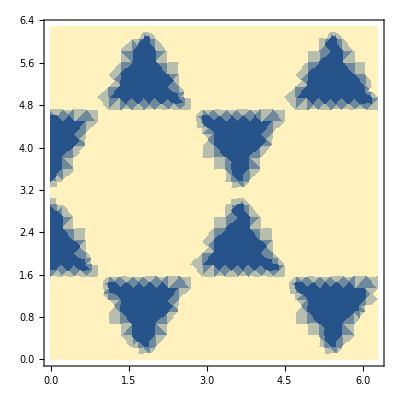

```mathematica
Block[{tvec={0,0.1,0}, λ=1, Δ={0,0},μ=1.007}, DensityPlot[ If[ Energies[tvec,λ,Δ,{kx,ky}][[9]]< μ,0.0,1.0], {kx,0,2π},{ky,0,2π}]]
```

```mathematica
regularPolygon[nbrSides_Integer?(#>2&),scale_: Norm[b1]]:=Polygon[scale {Cos[#],Sin[#]}&/@(2 Pi*Range[1/nbrSides,1,1/nbrSides])];
```

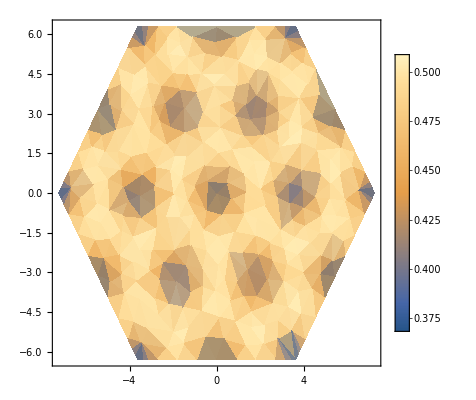

```mathematica
Block[{tvec={0,0.1,0}, λ=1, Δ={0,0},μ=1.007,n=6}, DensityPlot[ Fermi[100, Energies[tvec,λ,Δ,{kx,ky}][[9]]- μ],Element[{kx,ky},regularPolygon[n]],PlotLegends->Automatic,PlotRange->{0,1} ]]
```

### Bare Susceptibility Calculation

```mathematica
Fermi[β_,x_]:=Chop[N[ 1/(1+ Exp[ β x])]];
```

```mathematica
DFermi[β_,x_]:= Chop[N[D[ Fermi[β,x1],x1]/.{x1-> x}]];
```

```mathematica
Clear[FermiFactor];FermiFactor[tvec_,λ_,Δ_,β_,ω_,μ_,k_,q_,m_,n_]:= FermiFactor[tvec,λ,Δ,β,ω,μ,k,q,m,n]= Module[ {a = Energies[tvec,λ,Δ,k][[m]]-μ,b = Energies[tvec,λ,Δ,k+q][[n]]-μ}, (Fermi[β,b]-Fermi[β,a])/(ω+a-b+I 0.001)];
```

```mathematica
Clear[BSFactor];BSFactor[tvec_,λ_,Δ_,k_,q_,m_,n_,O1_,O2_]:= BSFactor[tvec,λ,Δ,k,q,m,n,O1,O2]= Module[ {u = Umat[tvec,λ,Δ,k], uq = Umat[tvec,λ,Δ,k+q]},(u†.O1.uq)[[m,n]] (uq†.O2.u)[[n,m]]];
```

```mathematica
Clear[Chi0q];Chi0q[bsp_, q_,O1_,O2_,β_,ω_,μ_,krange_]:= Chi0q[bsp,q,O1,O2,β,ω,μ,krange]= Chop[1/Length[kSpan[krange]] Sum[ Module[{tvec=bsp[[1]],λ=bsp[[2]], Δ=bsp[[3]]}, FermiFactor[tvec,λ,Δ,β,ω,μ,k,q,m,n]BSFactor[tvec,λ,Δ,k,q,m,n,O1,O2]],{k,kSpan[krange]},{m,1,12},{n,1,12}]];
```

```mathematica
Clear[Chi0qmax];Chi0qmax[bsp_, O1_,O2_,β_,ω_,μ_,krange_]:= Chi0qmax[bsp,O1,O2,β,ω,μ,krange]= Max[ Table[ Chi0q[bsp,q,O1,O2,β,ω,μ,krange],{q,kSpan[krange]}]];
```

#### Density-Density

```mathematica
O1 = IdentityMatrix[12]; O2=O1;
```

```mathematica
BetAB[ a_, b_] = Table[ (1-i)*a +i*b , {i,0.,1,0.01}];
```

```mathematica
kCut = Join[BetAB[ Gama,Kpoint]  ,BetAB[Kpoint,Mpoint], BetAB[Mpoint,Gama] ];
```

```mathematica
PlotChi0q[bsp_,β_,krange_,μ_,ω_] := Table[ Im[Chi0q[bsp,q,O1,O2,β,ω,μ,krange]] ,{q,kCut} ];
```

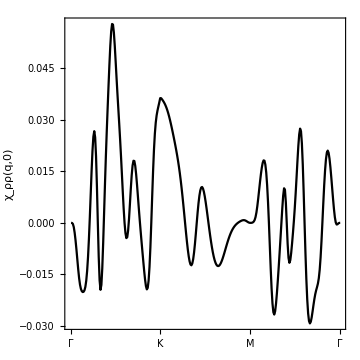

```mathematica
Block[ {bsp={{0,0.1,0},1,{0,0}},β=100,krange=10,μ=1.013,ω=0.0},ListPlot[ PlotChi0q[bsp,β,krange,μ,ω],PlotStyle->Black,
FrameTicks->{{{1,"Γ"},{101,"K"},{202,"M"},{303,"Γ"}},Automatic},Joined->True,FrameLabel->{None,"χ_ρρ(q,0)"},AspectRatio->1/1]]
```

#### Sz-Sz

The basis is {A,d_yz↑,A,d_yz↓,A,d_xz↑,A,d_xz↓,A,d_xy↑,A,d_xy↓,B,d_yz↑,B,d_yz↓,B,d_xz↑,B,d_xz↓,B,d_xy↑,B,d_xy↓}

```mathematica
O1 = KroneckerProduct[IdentityMatrix[6],PauliMatrix[3]]; O2=O1;
```

```mathematica
BetAB[ a_, b_] = Table[ (1-i)*a +i*b , {i,0.,1,0.01}];
```

```mathematica
kCut = Join[BetAB[ Gama,Kpoint]  ,BetAB[Kpoint,Mpoint], BetAB[Mpoint,Gama] ];
```

```mathematica
PlotChi0q[bsp_,β_,krange_,μ_,ω_] := Table[ Re[Chi0q[bsp,q,O1,O2,β,ω,μ,krange]] ,{q,kCut} ];
```

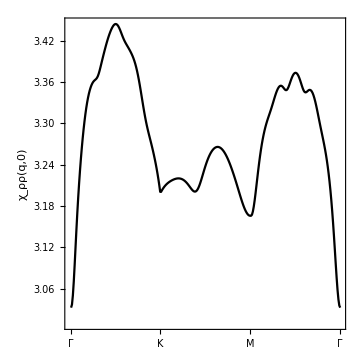

```mathematica
Block[ {bsp={{0,0.1,0},1,{0,0}},β=10,krange=10,μ=1.013,ω=0.0},ListPlot[ PlotChi0q[bsp,β,krange,μ,ω],PlotStyle->Black,
FrameTicks->{{{1,"Γ"},{101,"K"},{202,"M"},{303,"Γ"}},Automatic},Joined->True,FrameLabel->{None,"χ_ρρ(q,0)"},AspectRatio->1/1]]
```

#### All Possible Density/Spin/Sublattice

Order array = [density, Sx, Sy, Sz, A-B]

```mathematica
Oar = { IdentityMatrix[12], KroneckerProduct[IdentityMatrix[6],PauliMatrix[1]],KroneckerProduct[IdentityMatrix[6],PauliMatrix[2]],KroneckerProduct[IdentityMatrix[6],PauliMatrix[3]],KroneckerProduct[PauliMatrix[3],IdentityMatrix[6]]};
```

```mathematica
PlotChi0q[bsp_,β_,krange_,μ_,O1_,O2_] := Table[ Re[Chi0q[bsp,q,O1,O2,β,0.0,μ,krange]] ,{q,kCut} ];
```

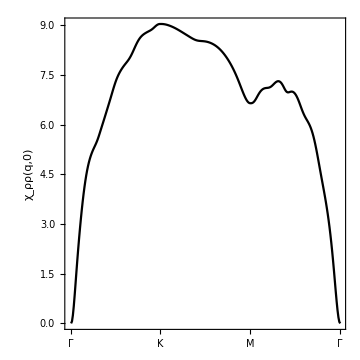
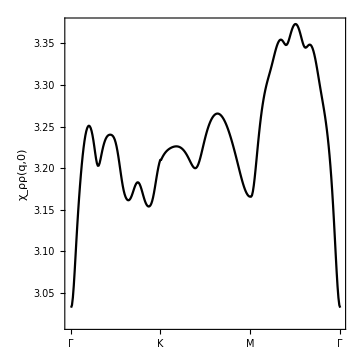
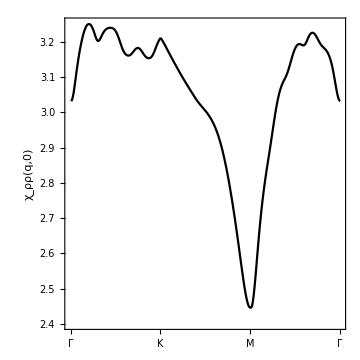
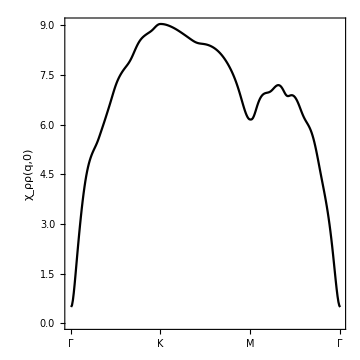
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
Table[ Module[ {bsp={{0,0.1,0},1,{0,0}},β=10,krange=10,μ=1.013,ω=0.0},ListPlot[ PlotChi0q[bsp,β,krange,μ,O1a,O1a],PlotStyle->Black,
FrameTicks->{{{1,"Γ"},{101,"K"},{202,"M"},{303,"Γ"}},Automatic},Joined->True,FrameLabel->{None,"χ_ρρ(q,0)"},AspectRatio->1/1]],{O1a,Oar}]
```